```mathematica
Clear[BuildFigure];
BuildFigure[id_,type_,pieces_List]:=
<|
Rule["id",id],
Rule["name",type],
Rule["category","animal"],
Rule["scale",1.0],
Rule["pieces",
BuildPiece[#,Part[pieces,#]]&/@Range[Length@pieces]
]
|>;
BuildFigure[name_String]:=Rule["Name",name]
```

```mathematica
BuildPiece[{pos_List,rot_Integer,mirror_Integer}]:=<|
Rule["position",pos],
Rule["rotation",rot],
Rule["flipped",mirror]
|>
```

```mathematica
BuildPiece[num_,{pos_List,rot_Integer,mirror_Integer}]:=<|
Rule["id",num],
Rule["shape",Lookup[
<|"1"->"TriangleLarge1","2"->"TriangleLarge2","3"->"TriangleSmall1","4"->"TriangleMedium","5"->"TriangleSmall2","6"->"Square","7"->"Parallelogram"|>,
ToString@num]],
Rule["position",pos],
Rule["rotation",rot],
Rule["flipped",mirror]
|>
```

```mathematica
First@First@ToExpression@$TangramData
```

{{253.12,352.15},3,0}

```mathematica
<<Tangrams`
```

```mathematica
num=1;
BuildFigure[num++,Last[#],Most[#]]&/@ToExpression@$TangramData
```

```mathematica
Export["TangramData.wl",]
```

TangramData.wl

```mathematica
fancyGrid/@Take[,3]
```

{id | 1
type | 3 Fishes 001
scale | 1.
pieces | {<|id→1,shape→TriangleLarge1,position→{253.12,352.15},rotation→3,flipped→0|>,<|id→2,shape→TriangleLarge2,position→{205.98,305.01},rotation→21,flipped→0|>,<|id→3,shape→TriangleSmall1,position→{232.31,149.71},rotation→6,flipped→0|>,<|id→4,shape→TriangleMedium,position→{333.59,432.63},rotation→18,flipped→0|>,<|id→5,shape→TriangleSmall2,position→{416.65,249.35},rotation→12,flipped→0|>,<|id→6,shape→Square,position→{499.98,249.35},rotation→0,flipped→1|>,<|id→7,shape→Parallelogram,position→{123.98,124.71},rotation→0,flipped→0|>},id | 2
type | Acrobat 001
scale | 1.
pieces | {<|id→1,shape→TriangleLarge1,position→{292.73,211.11},rotation→3,flipped→0|>,<|id→2,shape→TriangleLarge2,position→{245.59,352.53},rotation→15,flipped→0|>,<|id→3,shape→TriangleSmall1,position→{356.54,116.83},rotation→18,flipped→0|>,<|id→4,shape→TriangleMedium,position→{231.79,466.34},rotation→12,flipped→0|>,<|id→5,shape→TriangleSmall2,position→{245.59,281.82},rotation→9,flipped→0|>,<|id→6,shape→Square,position→{364.87,374.67},rotation→18,flipped→0|>,<|id→7,shape→Parallelogram,position→{269.16,435.02},rotation→15,flipped→1|>},id | 3
type | Acrobat 002
scale | 1.
pieces | {<|id→1,shape→TriangleLarge1,position→{311.17,345.74},rotation→9,flipped→0|>,<|id→2,shape→TriangleLarge2,position→{358.31,204.32},rotation→9,flipped→0|>,<|id→3,shape→TriangleSmall1,position→{372.12,110.04},rotation→18,flipped→0|>,<|id→4,shape→TriangleMedium,position→{330.7,284.79},rotation→0,flipped→0|>,<|id→5,shape→TriangleSmall2,position→{322.95,475.37},rotation→21,flipped→0|>,<|id→6,shape→Square,position→{430.45,367.88},rotation→18,flipped→0|>,<|id→7,shape→Parallelogram,position→{334.74,428.23},rotation→3,flipped→1|>}}

```mathematica
Export["TangramData.json",,"JSON"]
```

TangramData.json

```mathematica
square=Part[,1785]
```

<|id→1785,type→Square 001,scale→1.,pieces→{<|id→1,shape→TriangleLarge1,position→{233.33,299.33},rotation→0,flipped→0|>,<|id→2,shape→TriangleLarge2,position→{300,366},rotation→0,flipped→0|>,<|id→3,shape→TriangleSmall1,position→{300,266},rotation→0,flipped→0|>,<|id→4,shape→TriangleMedium,position→{366.67,232.67},rotation→0,flipped→0|>,<|id→5,shape→TriangleSmall2,position→{383.33,349.33},rotation→0,flipped→0|>,<|id→6,shape→Square,position→{350,299.33},rotation→0,flipped→0|>,<|id→7,shape→Parallelogram,position→{275,224.33},rotation→0,flipped→0|>}|>

```mathematica
colors=<|"TriangleLarge1"->Yellow,"TriangleLarge2"->Orange,"TriangleSmall1"->Green,"TriangleMedium"->Red,"TriangleSmall2"->LightGreen,"Square"->Gray,"Parallelogram"->Blue|>;
```

```mathematica
Association[Rule[#,#]&/@Lookup[Lookup[square,"pieces"],"shape"]]
```

<|TriangleLarge1→TriangleLarge1,TriangleLarge2→TriangleLarge2,TriangleSmall1→TriangleSmall1,TriangleMedium→TriangleMedium,TriangleSmall2→TriangleSmall2,Square→Square,Parallelogram→Parallelogram|>

```mathematica
sqPieces=Lookup[Lookup[square,"pieces"],{"shape","position"}]
```

{{TriangleLarge1,{233.33,299.33}},{TriangleLarge2,{300,366}},{TriangleSmall1,{300,266}},{TriangleMedium,{366.67,232.67}},{TriangleSmall2,{383.33,349.33}},{Square,{350,299.33}},{Parallelogram,{275,224.33}}}

```mathematica
{#,#}&/@sqPieces
```

{{{TriangleLarge1,{233.33,299.33}},{TriangleLarge1,{233.33,299.33}}},{{TriangleLarge2,{300,366}},{TriangleLarge2,{300,366}}},{{TriangleSmall1,{300,266}},{TriangleSmall1,{300,266}}},{{TriangleMedium,{366.67,232.67}},{TriangleMedium,{366.67,232.67}}},{{TriangleSmall2,{383.33,349.33}},{TriangleSmall2,{383.33,349.33}}},{{Square,{350,299.33}},{Square,{350,299.33}}},{{Parallelogram,{275,224.33}},{Parallelogram,{275,224.33}}}}

```mathematica
{colors[#[[1]]],Disk[#[[2]]]}&/@sqPieces
```

{{RGBColor[1, 1, 0],Disk[{233.33,299.33}]},{RGBColor[1, 0.5, 0],Disk[{300,366}]},{RGBColor[0, 1, 0],Disk[{300,266}]},{RGBColor[1, 0, 0],Disk[{366.67,232.67}]},{RGBColor[0.88, 1, 0.88],Disk[{383.33,349.33}]},{GrayLevel[0.5],Disk[{350,299.33}]},{RGBColor[0, 0, 1],Disk[{275,224.33}]}}

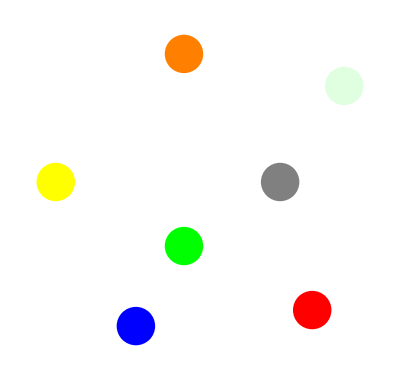

```mathematica
Graphics[{colors[#[[1]]],Disk[#[[2]],10]}&/@sqPieces]
```

## Math

```mathematica
getVertices[scale_]:=
Module[{a,b,c,d,e,f,g,h,i,j,res},
a={0,0};
b={0,-scale};
c={scale/2,-scale};
d={scale,-scale};
e={scale,-scale/2};
f={scale,0};
g={3*scale/4,-scale/4};
h={scale/2,-scale/2};
i={scale/4,-3*scale/4};
j={3*scale/4,-3*scale/4};
<|
Yellow->{a,b,h},
Orange->{a,f,h},
Green->{h,i,j},
Red->{c,d,e},
LightGreen->{e,f,g},
Gray->{h,j,e,g},
Blue->{b,c,j,i}
|>
]
```

```mathematica
verts=getVertices[1]
```

<|RGBColor[1, 1, 0]→{{0,0},{0,-1},{1/2,-1/2}},RGBColor[1, 0.5, 0]→{{0,0},{1,0},{1/2,-1/2}},RGBColor[0, 1, 0]→{{1/2,-1/2},{1/4,-3/4},{3/4,-3/4}},RGBColor[1, 0, 0]→{{1/2,-1},{1,-1},{1,-1/2}},RGBColor[0.88, 1, 0.88]→{{1,-1/2},{1,0},{3/4,-1/4}},GrayLevel[0.5]→{{1/2,-1/2},{3/4,-3/4},{1,-1/2},{3/4,-1/4}},RGBColor[0, 0, 1]→{{0,-1},{1/2,-1},{3/4,-3/4},{1/4,-3/4}}|>

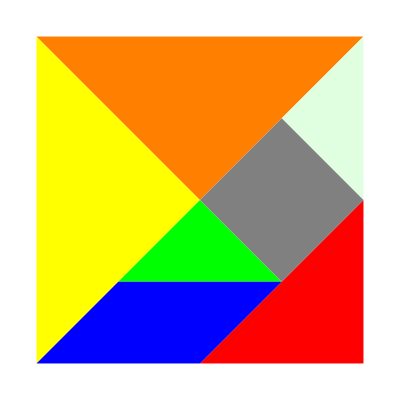

```mathematica
Graphics[{#,Polygon[verts[#]]}&/@Keys@verts]
```

```mathematica
With[{verts=getVertices[#]},Graphics[{#,Polygon[verts[#]]}&/@Keys@verts]]&/@Range[3]
```

{-Graphics-,-Graphics-,-Graphics-}